```mathematica
data=ToExpression@StringSplit@"0.3150000	0.2500000	0.2700000	0.4650000
1.7250000	1.3150000	1.4000000	2.0650000
11.7450000	9.0900000	9.9830000	11.3370000
11.2450000	7.6250000	7.6200000	10.3350000"
```

{0.315,0.25,0.27,0.465,1.725,1.315,1.4,2.065,11.745,9.09,9.983,11.337,11.245,7.625,7.62,10.335}

```mathematica
data1=Partition[data,4]
```

{{0.315,0.25,0.27,0.465},{1.725,1.315,1.4,2.065},{11.745,9.09,9.983,11.337},{11.245,7.625,7.62,10.335}}

```mathematica
Head[data[[1]]]
```

Real

```mathematica
data2=Transpose@Partition[data,4]
```

{{0.315,1.725,11.745,11.245},{0.25,1.315,9.09,7.625},{0.27,1.4,9.983,7.62},{0.465,2.065,11.337,10.335}}

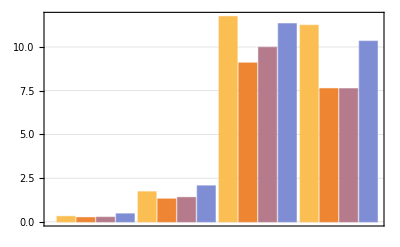

```mathematica
chart1=BarChart[data1,PlotTheme->"Detailed"]
```

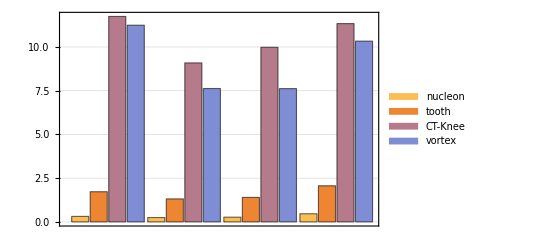

```mathematica
chart=BarChart[data2,ChartLegends->{"nucleon","tooth","CT-Knee","vortex"},PlotTheme->"Detailed"]
```

```mathematica
Export[NotebookDirectory[]<>"threads_chart.png",chart]
```

D:\document\work\time-varying-visualization\threads_chart.png

```mathematica
performance=StringSplit@"nucleon_Rainbow3_even	fixed	1.2849486	27	{0.0769653,0.103653,0.819382}	69	0.000304493

nucleon_Rainbow3_even	parallelsearch	0.3749850	3	{0.0769318,0.102995,0.820073}	40	0.000212413

nucleon_Rainbow3_even	linesearch	0.6099756	3	{0.076895,0.103191,0.819914}	18	0.000273971

nucleon_Rainbow5_even	fixed	1.4949402	29	{0.0166225,0.0163187,0.0665971,0.110839,0.789623}	80	0.00445178

nucleon_Rainbow5_even	parallelsearch	0.6749730	6	{0.0166625,0.0157522,0.0647695,0.104629,0.798186}	36	0.00170224

nucleon_Rainbow5_even	linesearch	1.1249550	6	{0.0166625,0.0157522,0.0647695,0.104629,0.798186}	36	0.00170224

nucleon_Rainbow7_even	fixed	0.8111688	14	{0.0175868,0.0166495,0.0157687,0.0710738,0.0690811,0.302786,0.49529}	80	0.00388667

nucleon_Rainbow7_even	parallelsearch	0.7955694	3	{0.0175958,0.0163524,0.0156808,0.0703116,0.0686603,0.291573,0.508061}	37	0.00189553

nucleon_Rainbow7_even	linesearch	0.6707742	3	{0.0175635,0.016404,0.0159079,0.0704844,0.0686585,0.295175,0.504042}	39	0.00260514

nucleon_Rainbow9_even	fixed	0.5927772	10	{0.0135309,0.00819539,0.0123186,0.0146587,0.0487674,0.0426849,0.0974428,0.463076,0.28756}	80	0.0036969

nucleon_Rainbow9_even	parallelsearch	1.1543556	3	{0.0133108,0.00778461,0.0116099,0.0146336,0.0487522,0.0422719,0.0960571,0.466722,0.287093}	39	0.003421

nucleon_Rainbow9_even	linesearch	0.7799700	3	{0.0133108,0.00778461,0.0116099,0.0146336,0.0487522,0.0422719,0.0960571,0.466722,0.287093}	39	0.003421

nucleon_Rainbow3_diagonal	fixed	1.1543556	23	{0.0157582,0.0578551,1.}	62	0.000690474

nucleon_Rainbow3_diagonal	parallelsearch	2.0279220	5	{0.0157744,0.0578548,1.}	25	0.000690474

nucleon_Rainbow3_diagonal	linesearch	0.9515634	5	{0.0157744,0.0578548,1.}	25	0.000690474

nucleon_Rainbow5_diagonal	fixed	2.9326872	59	{0.00114447,0.0084496,0.0398445,0.0916724,1.}	73	0.0272604

nucleon_Rainbow5_diagonal	parallelsearch	7.4722461	21	{0.00443725,0.00396807,0.0386577,0.0874549,1.}	40	0.0253909

nucleon_Rainbow5_diagonal	linesearch	2.8079820	20	{0.000851462,0.00839246,0.0399205,0.0910784,1.}	35	0.0269605

nucleon_Rainbow7_diagonal	fixed	4.1807732	79	{0.00286028,0.00545426,0.00859629,0.0516597,0.0685759,0.629929,1.}	80	0.0492066

nucleon_Rainbow7_diagonal	parallelsearch	12.4643201	23	{0.00286296,0.00578647,0.0077277,0.0480115,0.0643555,0.414437,1.}	40	0.018706

nucleon_Rainbow7_diagonal	linesearch	4.2899725	27	{0.00261839,0.00485421,0.00804228,0.0501203,0.0653662,0.481321,1.}	40	0.0293739

nucleon_Rainbow9_diagonal	fixed	-3.6785600855792691*10^9	0	{0.00264974,0.00476858,0.00662896,0.011467,0.0482928,0.058499,0.333125,1.,1.}	80	0.0526457

nucleon_Rainbow9_diagonal	parallelsearch	16.6762931	25	{0.00180442,0.00444864,0.00564692,0.00843018,0.0357705,0.0384093,0.125514,0.993582,1.}	39	0.0230999

nucleon_Rainbow9_diagonal	linesearch	4.6644598	27	{0.00320825,0.000546355,0.00627362,0.00891133,0.0369219,0.0400524,0.132339,0.996523,1.}	40	0.0249285

tooth_Rainbow3_even	fixed	8.8297132	29	{0.0616454,0.0636557,0.874699}	74	0.00026015

tooth_Rainbow3_even	parallelsearch	6.0060770	3	{0.0616335,0.0633585,0.875008}	17	0.0000316127

tooth_Rainbow3_even	linesearch	4.0404518	3	{0.0616299,0.0633587,0.875011}	27	0.0000316127

tooth_Rainbow5_even	fixed	5.1480660	14	{0.0423453,0.0628818,0.109365,0.299154,0.486254}	80	0.00114306

tooth_Rainbow5_even	parallelsearch	7.3788946	3	{0.042186,0.0625748,0.108417,0.29655,0.490272}	29	0.0000583743

tooth_Rainbow5_even	linesearch	4.7580610	3	{0.0422087,0.0625534,0.108475,0.296596,0.490167}	40	0.0000897322

tooth_Rainbow7_even	fixed	3.8688248	9	{0.0233132,0.27797,0.0315132,0.078885,0.0932007,0.274651,0.208702}	77	0.000449982

tooth_Rainbow7_even	parallelsearch	8.0340515	2	{0.0231046,0.277313,0.0315033,0.0789065,0.0931114,0.275508,0.208788}	24	0.000115083

tooth_Rainbow7_even	linesearch	3.8532247	2	{0.0230961,0.277324,0.0314999,0.0788765,0.0931224,0.275522,0.208794}	28	0.000115083

tooth_Rainbow9_even	fixed	2.4336000	5	{0.0237795,0.0492433,0.0522065,0.0294725,0.065237,0.0564179,0.204179,0.284187,0.223513}	79	0.000731899

tooth_Rainbow9_even	parallelsearch	7.5660000	1	{0.0237621,0.049204,0.0518642,0.0293362,0.0648683,0.056005,0.20275,0.286652,0.223793}	40	0.000247615

tooth_Rainbow9_even	linesearch	2.4648000	1	{0.0237621,0.049204,0.0518642,0.0293362,0.0648683,0.056005,0.20275,0.286652,0.223793}	40	0.000247615

tooth_Rainbow3_diagonal	fixed	7.4412000	24	{0.00930345,0.0262588,1.}	33	0.000638143

tooth_Rainbow3_diagonal	parallelsearch	13.0260000	4	{0.00942695,0.0261739,1.}	9	0.000638143

tooth_Rainbow3_diagonal	linesearch	4.6800000	4	{0.00942695,0.0261739,1.}	9	0.000638143

tooth_Rainbow5_diagonal	fixed	18.2364000	49	{0.00928934,0.0362207,0.113802,0.497456,1.}	80	0.020422

tooth_Rainbow5_diagonal	parallelsearch	22.8550066	8	{0.00845872,0.0335534,0.102769,0.408261,1.}	39	0.000689058

tooth_Rainbow5_diagonal	linesearch	12.2933516	8	{0.00861845,0.0334278,0.102763,0.408264,1.}	37	0.000689058

tooth_Rainbow7_diagonal	fixed	17.7218272	41	{0.00554907,0.25253,0.0341101,0.131697,0.229976,0.97202,1.}	80	0.0228015

tooth_Rainbow7_diagonal	parallelsearch	21.0602700	5	{0.00488034,0.183813,0.0309081,0.111858,0.184034,0.797573,1.}	40	0.00180395

tooth_Rainbow7_diagonal	linesearch	9.0325158	5	{0.00477717,0.183995,0.0307308,0.112008,0.184075,0.798574,1.}	40	0.001849

tooth_Rainbow9_diagonal	fixed	27.2845749	56	{0.00409082,0.0265015,0.0398259,0.0315932,0.106782,0.128157,0.72988,1.,1.}	80	0.0342815

tooth_Rainbow9_diagonal	parallelsearch	29.2969878	7	{0.00398447,0.0180019,0.0283944,0.0224417,0.0690815,0.0737959,0.410614,0.848391,1.}	40	0.00478758

tooth_Rainbow9_diagonal	linesearch	14.2272912	7	{0.00357379,0.0179171,0.0285034,0.0226199,0.0691774,0.074066,0.411491,0.851694,1.}	40	0.00475949
"
```

{nucleon_Rainbow3_even,fixed,1.2849486,27,{0.0769653,0.103653,0.819382},69,0.000304493,nucleon_Rainbow3_even,parallelsearch,0.3749850,3,{0.0769318,0.102995,0.820073},40,0.000212413,nucleon_Rainbow3_even,linesearch,0.6099756,3,{0.076895,0.103191,0.819914},18,0.000273971,nucleon_Rainbow5_even,fixed,1.4949402,29,{0.0166225,0.0163187,0.0665971,0.110839,0.789623},80,0.00445178,nucleon_Rainbow5_even,parallelsearch,0.6749730,6,{0.0166625,0.0157522,0.0647695,0.104629,0.798186},36,0.00170224,nucleon_Rainbow5_even,linesearch,1.1249550,6,{0.0166625,0.0157522,0.0647695,0.104629,0.798186},36,0.00170224,nucleon_Rainbow7_even,fixed,0.8111688,14,{0.0175868,0.0166495,0.0157687,0.0710738,0.0690811,0.302786,0.49529},80,0.00388667,nucleon_Rainbow7_even,parallelsearch,0.7955694,3,{0.0175958,0.0163524,0.0156808,0.0703116,0.0686603,0.291573,0.508061},37,0.00189553,nucleon_Rainbow7_even,linesearch,0.6707742,3,{0.0175635,0.016404,0.0159079,0.0704844,0.0686585,0.295175,0.504042},39,0.00260514,nucleon_Rainbow9_even,fixed,0.5927772,10,{0.0135309,0.00819539,0.0123186,0.0146587,0.0487674,0.0426849,0.0974428,0.463076,0.28756},80,0.0036969,nucleon_Rainbow9_even,parallelsearch,1.1543556,3,{0.0133108,0.00778461,0.0116099,0.0146336,0.0487522,0.0422719,0.0960571,0.466722,0.287093},39,0.003421,nucleon_Rainbow9_even,linesearch,0.7799700,3,{0.0133108,0.00778461,0.0116099,0.0146336,0.0487522,0.0422719,0.0960571,0.466722,0.287093},39,0.003421,nucleon_Rainbow3_diagonal,fixed,1.1543556,23,{0.0157582,0.0578551,1.},62,0.000690474,nucleon_Rainbow3_diagonal,parallelsearch,2.0279220,5,{0.0157744,0.0578548,1.},25,0.000690474,nucleon_Rainbow3_diagonal,linesearch,0.9515634,5,{0.0157744,0.0578548,1.},25,0.000690474,nucleon_Rainbow5_diagonal,fixed,2.9326872,59,{0.00114447,0.0084496,0.0398445,0.0916724,1.},73,0.0272604,nucleon_Rainbow5_diagonal,parallelsearch,7.4722461,21,{0.00443725,0.00396807,0.0386577,0.0874549,1.},40,0.0253909,nucleon_Rainbow5_diagonal,linesearch,2.8079820,20,{0.000851462,0.00839246,0.0399205,0.0910784,1.},35,0.0269605,nucleon_Rainbow7_diagonal,fixed,4.1807732,79,{0.00286028,0.00545426,0.00859629,0.0516597,0.0685759,0.629929,1.},80,0.0492066,nucleon_Rainbow7_diagonal,parallelsearch,12.4643201,23,{0.00286296,0.00578647,0.0077277,0.0480115,0.0643555,0.414437,1.},40,0.018706,nucleon_Rainbow7_diagonal,linesearch,4.2899725,27,{0.00261839,0.00485421,0.00804228,0.0501203,0.0653662,0.481321,1.},40,0.0293739,nucleon_Rainbow9_diagonal,fixed,-3.6785600855792691*10^9,0,{0.00264974,0.00476858,0.00662896,0.011467,0.0482928,0.058499,0.333125,1.,1.},80,0.0526457,nucleon_Rainbow9_diagonal,parallelsearch,16.6762931,25,{0.00180442,0.00444864,0.00564692,0.00843018,0.0357705,0.0384093,0.125514,0.993582,1.},39,0.0230999,nucleon_Rainbow9_diagonal,linesearch,4.6644598,27,{0.00320825,0.000546355,0.00627362,0.00891133,0.0369219,0.0400524,0.132339,0.996523,1.},40,0.0249285,tooth_Rainbow3_even,fixed,8.8297132,29,{0.0616454,0.0636557,0.874699},74,0.00026015,tooth_Rainbow3_even,parallelsearch,6.0060770,3,{0.0616335,0.0633585,0.875008},17,0.0000316127,tooth_Rainbow3_even,linesearch,4.0404518,3,{0.0616299,0.0633587,0.875011},27,0.0000316127,tooth_Rainbow5_even,fixed,5.1480660,14,{0.0423453,0.0628818,0.109365,0.299154,0.486254},80,0.00114306,tooth_Rainbow5_even,parallelsearch,7.3788946,3,{0.042186,0.0625748,0.108417,0.29655,0.490272},29,0.0000583743,tooth_Rainbow5_even,linesearch,4.7580610,3,{0.0422087,0.0625534,0.108475,0.296596,0.490167},40,0.0000897322,tooth_Rainbow7_even,fixed,3.8688248,9,{0.0233132,0.27797,0.0315132,0.078885,0.0932007,0.274651,0.208702},77,0.000449982,tooth_Rainbow7_even,parallelsearch,8.0340515,2,{0.0231046,0.277313,0.0315033,0.0789065,0.0931114,0.275508,0.208788},24,0.000115083,tooth_Rainbow7_even,linesearch,3.8532247,2,{0.0230961,0.277324,0.0314999,0.0788765,0.0931224,0.275522,0.208794},28,0.000115083,tooth_Rainbow9_even,fixed,2.4336000,5,{0.0237795,0.0492433,0.0522065,0.0294725,0.065237,0.0564179,0.204179,0.284187,0.223513},79,0.000731899,tooth_Rainbow9_even,parallelsearch,7.5660000,1,{0.0237621,0.049204,0.0518642,0.0293362,0.0648683,0.056005,0.20275,0.286652,0.223793},40,0.000247615,tooth_Rainbow9_even,linesearch,2.4648000,1,{0.0237621,0.049204,0.0518642,0.0293362,0.0648683,0.056005,0.20275,0.286652,0.223793},40,0.000247615,tooth_Rainbow3_diagonal,fixed,7.4412000,24,{0.00930345,0.0262588,1.},33,0.000638143,tooth_Rainbow3_diagonal,parallelsearch,13.0260000,4,{0.00942695,0.0261739,1.},9,0.000638143,tooth_Rainbow3_diagonal,linesearch,4.6800000,4,{0.00942695,0.0261739,1.},9,0.000638143,tooth_Rainbow5_diagonal,fixed,18.2364000,49,{0.00928934,0.0362207,0.113802,0.497456,1.},80,0.020422,tooth_Rainbow5_diagonal,parallelsearch,22.8550066,8,{0.00845872,0.0335534,0.102769,0.408261,1.},39,0.000689058,tooth_Rainbow5_diagonal,linesearch,12.2933516,8,{0.00861845,0.0334278,0.102763,0.408264,1.},37,0.000689058,tooth_Rainbow7_diagonal,fixed,17.7218272,41,{0.00554907,0.25253,0.0341101,0.131697,0.229976,0.97202,1.},80,0.0228015,tooth_Rainbow7_diagonal,parallelsearch,21.0602700,5,{0.00488034,0.183813,0.0309081,0.111858,0.184034,0.797573,1.},40,0.00180395,tooth_Rainbow7_diagonal,linesearch,9.0325158,5,{0.00477717,0.183995,0.0307308,0.112008,0.184075,0.798574,1.},40,0.001849,tooth_Rainbow9_diagonal,fixed,27.2845749,56,{0.00409082,0.0265015,0.0398259,0.0315932,0.106782,0.128157,0.72988,1.,1.},80,0.0342815,tooth_Rainbow9_diagonal,parallelsearch,29.2969878,7,{0.00398447,0.0180019,0.0283944,0.0224417,0.0690815,0.0737959,0.410614,0.848391,1.},40,0.00478758,tooth_Rainbow9_diagonal,linesearch,14.2272912,7,{0.00357379,0.0179171,0.0285034,0.0226199,0.0691774,0.074066,0.411491,0.851694,1.},40,0.00475949}

```mathematica
table=Partition[performance,7][[All,3;;4]]
```

{{1.2849486,27},{0.3749850,3},{0.6099756,3},{1.4949402,29},{0.6749730,6},{1.1249550,6},{0.8111688,14},{0.7955694,3},{0.6707742,3},{0.5927772,10},{1.1543556,3},{0.7799700,3},{1.1543556,23},{2.0279220,5},{0.9515634,5},{2.9326872,59},{7.4722461,21},{2.8079820,20},{4.1807732,79},{12.4643201,23},{4.2899725,27},{-3.6785600855792691*10^9,0},{16.6762931,25},{4.6644598,27},{8.8297132,29},{6.0060770,3},{4.0404518,3},{5.1480660,14},{7.3788946,3},{4.7580610,3},{3.8688248,9},{8.0340515,2},{3.8532247,2},{2.4336000,5},{7.5660000,1},{2.4648000,1},{7.4412000,24},{13.0260000,4},{4.6800000,4},{18.2364000,49},{22.8550066,8},{12.2933516,8},{17.7218272,41},{21.0602700,5},{9.0325158,5},{27.2845749,56},{29.2969878,7},{14.2272912,7}}

```mathematica
Length@table
```

48